```mathematica
(*inner3D computes the inner 2 integrals for the 3D FT in spherical coords*)
```

```mathematica
inner3D = 2 Pi Integrate[Exp[-2 Pi I k r Cos[θ]]*Sin[θ],{θ,0,Pi}]
```

(2 Sin[2 k π r])/(k r)

```mathematica
(*We can compute the FT of 1/r in this way*)
```

```mathematica
G=Limit[Assuming[{b>0, k>0},Integrate[Exp[-b r]/r inner3D r^2, {r,0,Infinity}]],b->0]
```

1/(k^2 π)

```mathematica
(*The FT of our de-sing kernel doesn't formally converge, but IBP of it does (the endpoints eval part ends up being 0 to satisfy that the result recovers FT of 1/r)*)
```

```mathematica
ibp = Simplify[D[r/Sqrt[r^2+a^2],r]]*Integrate[r inner3D,r]
```

-(a^2 Cos[2 k π r])/(k^2 π (a^2+r^2)^(3/2))

```mathematica
(*The FT of our de-sing kernel*)
```

```mathematica
ft3d1 = Assuming[{a>0, k>0},Integrate[-ibp, {r,0,Infinity}]]
```

(2 a BesselK[1,2 a k π])/k

```mathematica
(*Inverse FT recovers original de-sing kernel*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[ft3d1 inner3D k^2,{k,0,Infinity}]]
```

1/(√(a^2+r^2))

```mathematica
Limit[ft3d1,a->0]
```

1/(k^2 π)

```mathematica
(*We can use same process to calc FT of "high-order" de-sing kernels from vortex literature*)
```

```mathematica
ibp2 = Simplify[D[r(r^2+3/2a^2)/(r^2+a^2)^(3/2),r]]*Integrate[r inner3D,r]
```

-(3 a^4 Cos[2 k π r])/(2 k^2 π (a^2+r^2)^(5/2))

```mathematica
ft3d4 = Assuming[{a>0, k>0},Integrate[-ibp2, {r,0,Infinity}]]
```

2 a^2 π BesselK[2,2 a k π]

```mathematica
(*Verify that the IFT recovers our original de-sing kernel*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[ft3d4 inner3D k^2,{k,0,Infinity}]]
```

(3 a^2+2 r^2)/(2 (a^2+r^2)^(3/2))

```mathematica
(*Looking at the FT of the HO kernel, we notice a pattern of a^n k^(n-2) π^(n-1) BesselK[n,2 a k π] for n=1 and 2, what about n=3?*)
```

```mathematica
Assuming[{a>0, r>0},Integrate[a^3 k^1 π^2 BesselK[3,2 a k π] inner3D k^2,{k,0,Infinity}]]
```

(15 a^4+20 a^2 r^2+8 r^4)/(8 (a^2+r^2)^(5/2))

```mathematica
(*We can make a function to generate an arbitrary n-th version. Note that we need the coefficient on the highest power of 'r' to be 1, so that when a=0 we recover 1/r. Inspection tells us that we need to multiply the IFT of our pattern by (2/(n-1)!) to get the coefficient to be 1*)
```

```mathematica
DeSingKernel[n_]:= (2/(n-1)!)*Assuming[{a>0, r>0},Integrate[a^n k^(n-2) π^(n-1) BesselK[n,2 a k π] inner3D k^2,{k,0,Infinity}]]
```

```mathematica
(*Alternate approach to computing FT of de-sing kernel that I'm not sure quite works*)
```

```mathematica
inner3Dexp=Expand[TrigToExp[inner3D]*Exp[-b r]]
```

(ⅈ ⅇ^(-b r-2 ⅈ k π r))/(k r)-(ⅈ ⅇ^(-b r+2 ⅈ k π r))/(k r)

```mathematica
ft3d2 = Limit[Assuming[{k>0, a>0, b>0},Integrate[(1/Sqrt[r^2+a^2])inner3Dexp r^2,{r,0,Infinity}]],b->0]
```

(4+ⅈ a k π^2 BesselY[1,-2 ⅈ a k π]-ⅈ a k π^2 BesselY[1,2 ⅈ a k π])/(2 k^2 π)

```mathematica
ft3d3 = Limit[Assuming[{k>0, a>0, b>0},Integrate[((r^2+3/2a^2)/(r^2+a^2)^(3/2))inner3Dexp r^2,{r,0,Infinity}]],b->0]
```

-3/2 a^2 π^2 (BesselY[0,-2 ⅈ a k π]+BesselY[0,2 ⅈ a k π])

```mathematica
(*Looking at the decay of derivatives of the de-sing kernel shows us that we don't need to do fancy tricks to compute the FT, it converges properly:*)
```

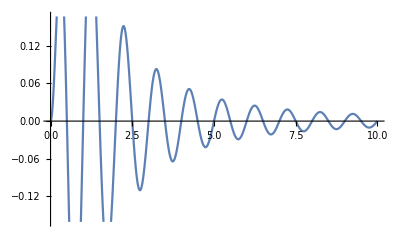

```mathematica
Plot[(1r/(r^2+1^2)^(3/2))*Sin[2 Pi 1r],{r,0,10}]
```

```mathematica
(*Function that computes the FT of 'f'*)
```

```mathematica
FT[f_]:=Assuming[{d>0, k>0},Integrate[f inner3D r^2 ,{r,0,Infinity}]]
```

```mathematica
(*Function that computes the FT of the m-th series expansion of the n-th de-sing kernel. We need to do some tricks so that the FT doesn't choke: First, we leave out the FT of the 0th series term and tack it on at the end (since it requires special handling wrt it's FT). Second, we use List@@Apart[] to break the series expansion into a list of individual terms based on the exponent of 'r' and compute the FT of each separately. *)
```

```mathematica
Fdesing[n_,m_]:=Total[FT[List@@Apart[Normal[Series[DeSingKernel[n],{a,d,m}]]/.a->0,r][[1;;-(n+1)]]]] + ((2/(n-1)!)d^n k^(n-2) π^(n-1) BesselK[n,2 d k π])
```

```mathematica
Assuming[d>0,Integrate[(G-Fdesing[1,5])^2,{k,0,Infinity}]]
```

(3059 d^3 π^3)/1048576

```mathematica
Assuming[d>0,Integrate[(G-Fdesing[2,5])^2,{k,0,Infinity}]]
```

(49021 d^3 π^3)/33554432

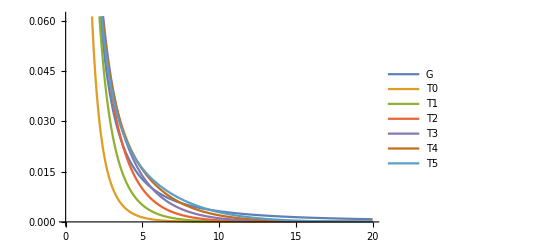

```mathematica
Plot[Evaluate@({G,T}/.d->0.1),{k,0,20},PlotLegends->{"G","T0","T1","T2","T3","T4","T5"}]
```

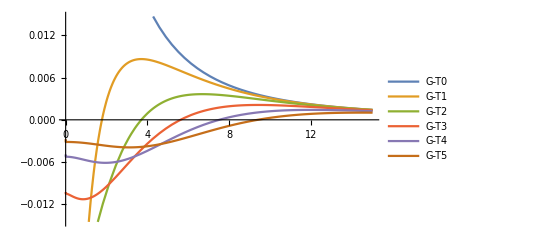

```mathematica
Plot[Evaluate@(G-T/.d->0.1),{k,0,15},PlotLegends->{"G-T0","G-T1","G-T2","G-T3","G-T4","G-T5"}]
```

```mathematica
Assuming[{k>=0},Series[Fdesing[1,5],{d,0,5}]]
```

1/(k^2 π)+(π d^2)/10+1/20 k^2 π^3 d^4+O[d]^6

```mathematica
Assuming[{k>=0},Series[Fdesing[2,5],{d,0,5}]]
```

1/(k^2 π)-1/20 (k^2 π^3) d^4+O[d]^6

```mathematica
Assuming[{k>=0},Series[Fdesing[3,7],{d,0,7}]]
```

1/(k^2 π)+1/252 k^4 π^5 d^6+O[d]^8

```mathematica
u=Sin[Pi x]Sin[Pi y]Sin[Pi z]/(-3 Pi^2)
```

-(Sin[π x] Sin[π y] Sin[π z])/(3 π^2)

```mathematica
ff=Laplacian[u,{x,y,z}]
```

Sin[π x] Sin[π y] Sin[π z]

```mathematica
FortranForm[Normal[Series[DeSingKernel[1],{a,d,3}]]/.{a->0,d^2+r^2->k}]
```

d**2/k**1.5 + 1/Sqrt(k) + (d**2*(2*d**2 - r**2))/(2.*k**2.5) - (d**3*(-2*d**3 + 3*d*r**2))/(2.*k**3.5)

```mathematica
FortranForm[Normal[Series[DeSingKernel[2],{a,d,5}]]/.{a->0,d^2+r^2->k}]
```

(3*d**4)/(2.*k**2.5) + (3*d**2 + 2*r**2)/(2.*k**1.5) + (3*d**2*(2*d**4 - 3*d**2*r**2))/(4.*k**3.5) + (d**4*(6*d**4 - 23*d**2*r**2 + 6*r**4))/(4.*k**4.5) + 
     -  (3*d**6*(8*d**6 - 88*d**4*r**2 + 115*d**2*r**4 - 20*r**6))/(16.*k**6.5) + (3*d**4*(8*d**6 - 56*d**4*r**2 + 39*d**2*r**4 - 2*r**6))/(16.*k**5.5)

```mathematica
FortranForm[Normal[Series[DeSingKernel[3],{a,d,7}]]/.{a->0,d^2+r^2->k}]
```

(15*d**6)/(8.*k**3.5) + (15*d**2*(2*d**6 - 5*d**4*r**2))/(16.*k**4.5) + (15*d**4 + 20*d**2*r**2 + 8*r**4)/(8.*k**2.5) + (5*d**3*(6*d**7 - 37*d**5*r**2 + 20*d**3*r**4))/(16.*k**5.5) + 
     -  (15*d**4*(8*d**8 - 88*d**6*r**2 + 115*d**4*r**4 - 20*d**2*r**6))/(64.*k**6.5) + (3*d**5*(40*d**9 - 680*d**7*r**2 + 1563*d**5*r**4 - 680*d**3*r**6 + 40*d*r**8))/(64.*k**7.5) + 
     -  (5*d**6*(48*d**10 - 1160*d**8*r**2 + 4078*d**6*r**4 - 3195*d**4*r**6 + 520*d**2*r**8 - 8*r**10))/(128.*k**8.5) + 
     -  (15*d**7*(16*d**11 - 520*d**9*r**2 + 2578*d**7*r**4 - 3143*d**5*r**6 + 980*d**3*r**8 - 56*d*r**10))/(128.*k**9.5)

```mathematica
k6s7=Normal[Series[DeSingKernel[3],{a,d,7}]]/.{a->0}
```

(15 d^6)/(8 (d^2+r^2)^(7/2))+(15 d^2 (2 d^6-5 d^4 r^2))/(16 (d^2+r^2)^(9/2))+(15 d^4+20 d^2 r^2+8 r^4)/(8 (d^2+r^2)^(5/2))+(5 d^3 (6 d^7-37 d^5 r^2+20 d^3 r^4))/(16 (d^2+r^2)^(11/2))+(15 d^4 (8 d^8-88 d^6 r^2+115 d^4 r^4-20 d^2 r^6))/(64 (d^2+r^2)^(13/2))+(3 d^5 (40 d^9-680 d^7 r^2+1563 d^5 r^4-680 d^3 r^6+40 d r^8))/(64 (d^2+r^2)^(15/2))+(5 d^6 (48 d^10-1160 d^8 r^2+4078 d^6 r^4-3195 d^4 r^6+520 d^2 r^8-8 r^10))/(128 (d^2+r^2)^(17/2))+(15 d^7 (16 d^11-520 d^9 r^2+2578 d^7 r^4-3143 d^5 r^6+980 d^3 r^8-56 d r^10))/(128 (d^2+r^2)^(19/2))

```mathematica
dsk3=DeSingKernel[3]
```

(15 a^4+20 a^2 r^2+8 r^4)/(8 (a^2+r^2)^(5/2))

```mathematica
PltVar[v_,aa_]:=Plot[{Abs[D[k6s7/.d->0.8,{r,v}]],Abs[D[dsk3/.a->aa,{r,v}]]}//Evaluate,{r,0,0.5},PlotRange->All,PlotLegends->Automatic]
```

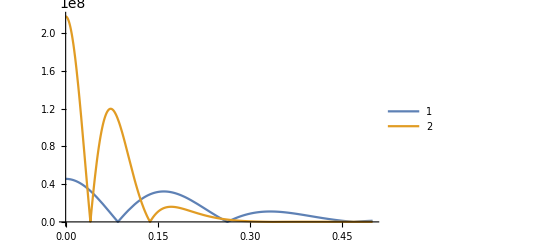

```mathematica
PltVar[6,0.2]
```

```mathematica
OptV[n_]:=Plot[{v*(n-2v-1)^(2v+1)}//Evaluate,{v,1,20},PlotRange->All]
```

```mathematica
OptV[50]
```

-Graphics-

```mathematica
TVa[p_,v_,k_]:=Abs[Simplify[D[Simplify[D[DeSingKernel[k]/.a->d,{d,p}]]*((-d)^p)/p!,{r,v+1}]]]
```

```mathematica
TV[p_,v_,k_]:=Assuming[d>0,Integrate[TVa[p,v,k],{r,-1,1}]]
```

```mathematica
TVd[p_,v_,k_,dd_]:=NIntegrate[TVa[p,v,k]/.d->dd,{r,-1,1}]
```

```mathematica
TV[1,1,3]
```

Piecewise[{{35840/(6561 d^2), d==2 √2||d≤0}, {(105 d^6)/(4 (1+d^2)^(9/2)), d>2 √2}, {(35 (-19683 d^8+8192 √(1+d^2)+32768 d^2 √(1+d^2)+49152 d^4 √(1+d^2)+32768 d^6 √(1+d^2)+8192 d^8 √(1+d^2)))/(26244 d^2 (1+d^2)^(9/2)), True}}]

```mathematica
Table[TVd[p,1,3,0.05],{p,0,7}]
```

{1944.63,4370.07,7310.79,10852.1,14925.3,19502.1,24564.5,30100.}

```mathematica
Table[TVd[p,2,3,0.05],{p,0,7}]
```

{104513.,355752.,786863.,1.43651×10^6,2.33757×10^6,3.52161×10^6,5.01918×10^6,6.86015×10^6}

```mathematica
Table[TVd[p,3,3,0.05],{p,0,7}]
```

{8.37999×10^6,3.72775×10^7,1.01881×10^8,2.20516×10^8,4.14291×10^8,7.06975×10^8,1.12492×10^9,1.69702×10^9}

```mathematica
Table[TVd[p,6,3,0.05],{p,0,7}]
```

{1.60364×10^13,1.20092×10^14,5.10434×10^14,1.61831×10^15,4.2565×10^15,9.81508×10^15,2.05093×10^16,3.96847×10^16}

```mathematica
Table[TVd[p,7,3,0.05],{p,0,7}]
```

{2.70123×10^15,2.29461×10^16,1.09044×10^17,3.82127×10^17,1.10061×10^18,2.75773×10^18,6.22089×10^18,1.29227×10^19}

```mathematica
Table[TVd[p,8,3,0.05],{p,0,7}]
```

{5.11792×10^17,4.86135×10^18,2.55383×10^19,9.80156×10^19,3.06803×10^20,8.3001×10^20,2.01035×10^21,4.46238×10^21}

```mathematica
Table[TVd[p,9,3,0.05],{p,0,7}]
```

{1.07637×10^20,1.13035×10^21,6.50412×10^21,2.71317×10^22,9.17055×10^22,2.66412×10^23,6.89579×10^23,1.6289×10^24}

```mathematica
Table[TVd[p,12,3,0.05],{p,0,7}]
```

{1.70323×10^27,2.30036×10^28,1.66893×10^29,8.63076×10^29,3.5641×10^30,1.24899×10^31,3.85629×10^31,1.07583×10^32}

```mathematica
TVErr[V_,v_,n_]:=(32/15)*(V/(Pi*v*(n-2v-1)^(2v+1)))
```

```mathematica
TVErr[Total[Out[67]],1,55]
```

0.54848

```mathematica
TVErr[Total[Out[68]],2,55]
```

0.0221886

```mathematica
TVErr[Total[Out[69]],3,55]
```

0.00166228

```mathematica
TVErr[Total[Out[79]],6,55]
```

6.84465×10^-6

```mathematica
TVErr[Total[Out[81]],8,55]
```

9.14436×10^-7

```mathematica
TVErr[Total[Out[85]],12,55]
```

1.09034×10^-6